```mathematica
UnitForm[units_][quantity_]:=UnitConvert[quantity,units]
```

### Constants

```mathematica
filters={"Blue","Yellow","Red","NoFilter"};
colorFilters=filters[[;;3]];
colorWavelengths=Quantity[{4495,5490,6500},"Angstroms"];
color=<|"NoFilter"->(Gray&),"Red"->(Red&),"Blue"->(Blue&),"Yellow"->(Green&)|>;
samples={"White","BK7","SF58"};
sampleThickness=Quantity[{1.036,0.956,1.272},"cm"];
magnetism={5,-90,-166,-259,-5,83,167,243};
```

### Hysteresis

```mathematica
{{0, 0, 0.69}, {5.6, 0.23, 46.33}, {10.1, 0.42, 88.14}, {15.2, 0.64, 127.26}, {20.4, 0.85, 170.02}, {24.9, 1.04, 204.09}, {30.4, 1.27, 250.5}, {24.7, 1.03, 213.04}, {20.3, 0.84, 178.63}, {15.2, 0.63, 132.31}, {10.1, 0.42, 91.1}, {5.6, 0.23, 52.94}, {0, 0, 5.51}, {-5.1, -0.21, -39.8}, {-10.2, -.42, -90.45}, {-15.2, -.63, -124.39}, {-20.4, -.85, -165.92}, {-25, -1.04, -201.95}, {-30, -1.26, -259.3}, {-25, -1.03, -209.86}, {-20.2, -.83, -180.19}, {-15, -.62, -130.42}, {-10.2, -.42, -91.94}, {-5.1, -.21, -48.81}, {0, 0, -5.18}, {5, 0.2, 37.81}, {10.2, 0.42, 83.00}, {14.9, .62, 119.29}, {20.4, .84, 166.92}, {24.9, 1.03, 211.65}, {30.5, 1.26, 243.7}}ᵀ;
{V,A,B}=Quantity@@@({%,{"Volts","Amps","Milliteslas"}}ᵀ)
```

{{0 V,5.6 V,10.1 V,15.2 V,20.4 V,24.9 V,30.4 V,24.7 V,20.3 V,15.2 V,10.1 V,5.6 V,0 V,-5.1 V,-10.2 V,-15.2 V,-20.4 V,-25 V,-30 V,-25 V,-20.2 V,-15 V,-10.2 V,-5.1 V,0 V,5 V,10.2 V,14.9 V,20.4 V,24.9 V,30.5 V},{0 A,0.23 A,0.42 A,0.64 A,0.85 A,1.04 A,1.27 A,1.03 A,0.84 A,0.63 A,0.42 A,0.23 A,0 A,-0.21 A,-0.42 A,-0.63 A,-0.85 A,-1.04 A,-1.26 A,-1.03 A,-0.83 A,-0.62 A,-0.42 A,-0.21 A,0 A,0.2 A,0.42 A,0.62 A,0.84 A,1.03 A,1.26 A},{0.69 mT,46.33 mT,88.14 mT,127.26 mT,170.02 mT,204.09 mT,250.5 mT,213.04 mT,178.63 mT,132.31 mT,91.1 mT,52.94 mT,5.51 mT,-39.8 mT,-90.45 mT,-124.39 mT,-165.92 mT,-201.95 mT,-259.3 mT,-209.86 mT,-180.19 mT,-130.42 mT,-91.94 mT,-48.81 mT,-5.18 mT,37.81 mT,83. mT,119.29 mT,166.92 mT,211.65 mT,243.7 mT}}

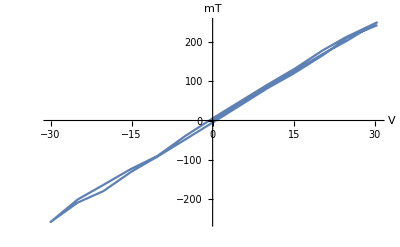

```mathematica
ListPlot[{V,B}ᵀ,Joined->True,AxesLabel->Automatic]
```

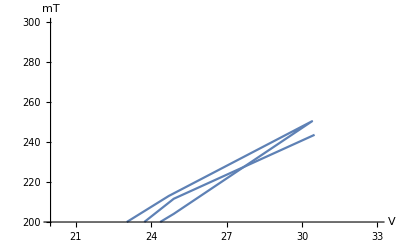

```mathematica
ListPlot[{V,B}ᵀ,Joined->True,PlotRange->{{20,33},{200,300}},AxesLabel->Automatic]
```

### Malus Law

```mathematica
FitMalusFull[filter_]:=
Module[{rawData,n,chunks,μ,σ,around,angles},
rawData=Rest[Import[NotebookDirectory[]<>"Malus"<>filter<>".xlsx","XLSX"][[1]]]ᵀ[[2]];
n=Length@rawData/10-1;
{μ,σ}=Table[#@rawData[[10i+1;;10i+10]]&/@{Mean,StandardDeviation},{i,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
angles=Range[0,10n+1,10]°;
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)]
(*Print[fit];
Print[fit["ParameterTable"]];
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,0,angles[[-1]]},ColorFunction->color[filter]]
]*)
]
```

```mathematica
π/2+Subscript[m, 3]/.FitMalusFull["Blue"]["BestFitParameters"]
```

2.67547

FittedModel[-0.0015013-0.0385886 Cos[1.10467-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.0015013 | 0.000017872 | -84.0031 | 5.10037×10^-41
m_2 | 0.0385886 | 0.0000206507 | 1868.63 | 8.63509×10^-87
m_3 | 1.10467 | 0.00049499 | 2231.71 | 2.06263×10^-89

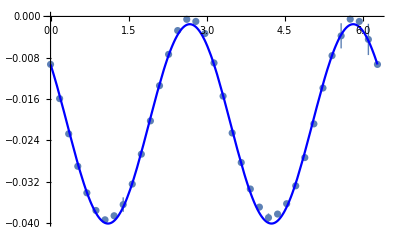

```mathematica
FitMalusFull[filters[[1]]]
```

FittedModel[-0.00061743-0.0390204 Cos[1.10733-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.00061743 | 6.10432×10^-6 | -101.146 | 9.46303×10^-44
m_2 | 0.0390204 | 0.0000179432 | 2174.67 | 4.97455×10^-89
m_3 | 1.10733 | 0.000241489 | 4585.45 | 4.79912×10^-100

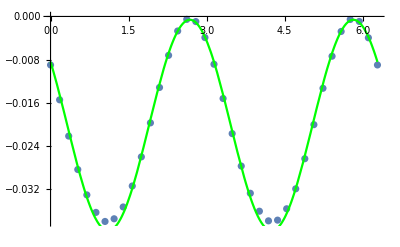

```mathematica
FitMalusFull[filters[[2]]]
```

```mathematica
field[i_]:=magnetism[[Floor[i/9]+1]];
sample[i_]:=samples[[Mod[Floor[i/3],3]+1]];
filter[i_]:=colorFilters[[Mod[i,3]+1]];
startAngles=Table@@@{{195, 9}, {190, 2}, {195, 4}, {200, 3}, {180, 1}, {190, 2}, {200, 1}, {195, 2}, {200, 3}, {175, 1}, {185, 1}, {190, 1}, {200, 1}, {195, 1}, {200, 4}, {195, 1}, {200, 5}, {195, 3}, {200, 9}, {210, 3}, {200, 3}, {195, 2}, {200, 1}, {220, 1}, {215, 2}, {195, 1}, {205, 1}, {190, 2}, {195, 2}}//Flatten;
minAngles=Import[NotebookDirectory[]<>"MinAngleEye.xlsx","XLSX"][[1]]ᵀ[[1]]
```

{153.,153.,154.,151.,151.,155.,154.,154.,152.,146.,148.,150.,152.,153.,149.,156.,156.,154.,135.,143.,144.,155.,150.,150.,155.,155.,154.,130.,139.,144.,156.,151.,154.,157.,157.,158.,151.,158.,153.,155.,151.,151.,149.,150.,152.,160.,159.,157.,156.,155.,154.,155.,152.,151.,165.,163.,161.,154.,154.,155.,149.,149.,152.,175.,167.,163.,148.,159.,146.,143.,147.,148.}

```mathematica
Table[{i,field@i,sample@i,filter@i,startAngles[[i+1]]},{i,0,8*9-1}]//TableForm
```

0 | 5 | White | Blue | 195
1 | 5 | White | Yellow | 195
2 | 5 | White | Red | 195
3 | 5 | BK7 | Blue | 195
4 | 5 | BK7 | Yellow | 195
5 | 5 | BK7 | Red | 195
6 | 5 | SF58 | Blue | 195
7 | 5 | SF58 | Yellow | 195
8 | 5 | SF58 | Red | 195
9 | -90 | White | Blue | 190
10 | -90 | White | Yellow | 190
11 | -90 | White | Red | 195
12 | -90 | BK7 | Blue | 195
13 | -90 | BK7 | Yellow | 195
14 | -90 | BK7 | Red | 195
15 | -90 | SF58 | Blue | 200
16 | -90 | SF58 | Yellow | 200
17 | -90 | SF58 | Red | 200
18 | -166 | White | Blue | 180
19 | -166 | White | Yellow | 190
20 | -166 | White | Red | 190
21 | -166 | BK7 | Blue | 200
22 | -166 | BK7 | Yellow | 195
23 | -166 | BK7 | Red | 195
24 | -166 | SF58 | Blue | 200
25 | -166 | SF58 | Yellow | 200
26 | -166 | SF58 | Red | 200
27 | -259 | White | Blue | 175
28 | -259 | White | Yellow | 185
29 | -259 | White | Red | 190
30 | -259 | BK7 | Blue | 200
31 | -259 | BK7 | Yellow | 195
32 | -259 | BK7 | Red | 200
33 | -259 | SF58 | Blue | 200
34 | -259 | SF58 | Yellow | 200
35 | -259 | SF58 | Red | 200
36 | -5 | White | Blue | 195
37 | -5 | White | Yellow | 200
38 | -5 | White | Red | 200
39 | -5 | BK7 | Blue | 200
40 | -5 | BK7 | Yellow | 200
41 | -5 | BK7 | Red | 200
42 | -5 | SF58 | Blue | 195
43 | -5 | SF58 | Yellow | 195
44 | -5 | SF58 | Red | 195
45 | 83 | White | Blue | 200
46 | 83 | White | Yellow | 200
47 | 83 | White | Red | 200
48 | 83 | BK7 | Blue | 200
49 | 83 | BK7 | Yellow | 200
50 | 83 | BK7 | Red | 200
51 | 83 | SF58 | Blue | 200
52 | 83 | SF58 | Yellow | 200
53 | 83 | SF58 | Red | 200
54 | 167 | White | Blue | 210
55 | 167 | White | Yellow | 210
56 | 167 | White | Red | 210
57 | 167 | BK7 | Blue | 200
58 | 167 | BK7 | Yellow | 200
59 | 167 | BK7 | Red | 200
60 | 167 | SF58 | Blue | 195
61 | 167 | SF58 | Yellow | 195
62 | 167 | SF58 | Red | 200
63 | 243 | White | Blue | 220
64 | 243 | White | Yellow | 215
65 | 243 | White | Red | 215
66 | 243 | BK7 | Blue | 195
67 | 243 | BK7 | Yellow | 205
68 | 243 | BK7 | Red | 190
69 | 243 | SF58 | Blue | 190
70 | 243 | SF58 | Yellow | 195
71 | 243 | SF58 | Red | 195

```mathematica
ClearAll@FitFaradata
geti[field_,sample_,filter_]:=3^2(Position[magnetism,field][[1,1]]-1)+3(Position[samples,sample][[1,1]]-1)+Position[colorFilters,filter][[1,1]]-1;
(*FitFaradata[field_,sample_,filter_,opts:OptionsPattern[{plot->False,params->False}]]:=FitFaradata[
3^2(Position[magnetism,field][[1,1]]-1)+3(Position[samples,sample][[1,1]]-1)+Position[colorFilters,filter][[1,1]]-1,
opts
];*)
(*FitFaradata[i_,opts:OptionsPattern[{plot->False,params->False}]]:=*)
FitFaradata[field_,sample_,filter_,opts:OptionsPattern[{plot->False,params->False}]]:=Module[
{
angleStart=startAngle[geti[field,sample,filter]],
rawData,n,chunks,μ,σ,around,angles
},
(*Print[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx"];*)
rawData=Rest[Import[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx","XLSX"][[1]]]ᵀ[[2]];
startAngle=startAngles[[0+1]];
n=Length@rawData/10-1;
{angles,μ,σ}=Table[Join[{startAngle-10j}°,#@rawData[[10j+1;;10j+10]]&/@{Mean,StandardDeviation}],{j,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
(*Print[fit];*)
If[OptionValue[params],
Print[fit["ParameterTable"]]
];
If[OptionValue[plot],
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,angles[[1]],angles[[-1]]},ColorFunction->color[filter]]
]
];
fit
]
```

```mathematica
Flatten[Table[{field,Subscript[m, 3]/.FitFaradata[field,"White",filter]["BestFitParameters"]},{field,magnetism},{filter,colorFilters}],1]
```

{{5,1.10421},{5,1.10197},{5,1.10734},{-90,1.06093},{-90,1.10996},{-90,1.04045},{-166,1.09471},{-166,1.02581},{-166,1.06908},{-259,1.0938},{-259,1.04254},{-259,1.02416},{-5,1.10421},{-5,1.10197},{-5,1.10734},{83,1.14168},{83,1.09825},{83,1.07686},{167,1.09405},{167,0.998416},{167,0.958192},{243,1.03734},{243,0.990327},{243,0.921439}}

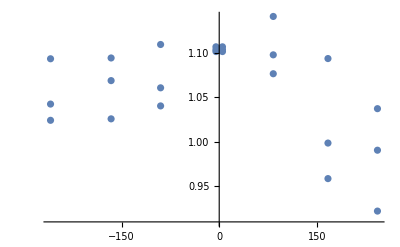

```mathematica
ListPlot[%]
```

```mathematica
Table[{field,θ/.FindMaximum[FitFaradata[field,"White","Blue"]//Normal,{θ,2.7}][[2]]},{field,magnetism}]
(*Flatten[□,1]*)
```

{{5,2.67501},{-90,2.63173},{-166,2.6655},{-259,2.6646},{-5,2.67501},{83,2.71248},{167,2.66484},{243,2.60814}}

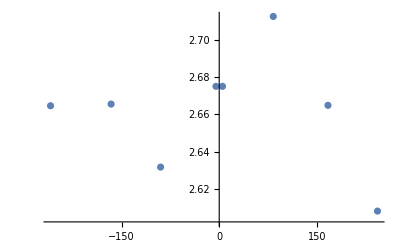

```mathematica
ListPlot[%]
```